# n - Laman graphs

This Mathematica notebook focuses on the generation, validation, and cataloging of generalized Laman graphs.

1. Standard 2-Laman Graph Generation: Implements recursive generation of Laman graphs using Henneberg moves, fundamental operations that expand the graph while maintaining its rigidity properties, based on a nice code from J. Kulp.

2. n-Laman Graph Validation: Contains functions to assess if a given graph qualifies as an n-Laman graph, an extension of the Laman graph concept, as introduced in a recent article (https://arxiv.org/abs/2207.14321).

3. n-Laman Graph Database Compilation: Initiates the creation of a database for n-Laman graphs, employing Mathematica’s GraphData. This section aims to systematically compile instances of n-Laman graphs, though it is noted to be an incomplete database due to the inherent limitations of GraphData.

### Generating and Manipulating 2-Laman Graphs

```mathematica
Clear[lamanSubgraphTestQ,lamanQ,hennMove1, hennMove2, hennApply]
(* Laman graph tests *)
lamanSubgraphTestQ[g_Graph]:=EdgeCount[g]≤2 VertexCount[g]-3;
lamanQ[g_Graph]:=(EdgeCount[g]==2 VertexCount[g]-3)&&(And@@Map[lamanSubgraphTestQ[Subgraph[g,#]]&][Subsets[VertexList[g],{2,VertexCount[g]}]])

(* Henneberg moves (naming convention from Wikipedia) *)
(* Apply Henneberg move that adds a vertex. *)
hennMove1[g_Graph,{v1_,v2_}]:=Block[
{new},
EdgeAdd[VertexAdd[g,new],{v1<->new,v2<->new}]//CanonicalGraph
]
hennMove1[g_Graph,{v1_,v2_},"directed"]:=Block[
{new},
EdgeAdd[VertexAdd[g,new],{v1->new,new->v2}](*//CanonicalGraph*)
]
(* Henneberg move that splits an edge *)
hennMove2[g_Graph,{e_,v_}]:=Module[
{new},
CanonicalGraph[EdgeAdd[VertexAdd[EdgeDelete[g,e],new],{v<->new,List@@e[[1]]<->new,List@@e[[2]]<->new}]]
]
(* Apply Henneberg moves to a graph in all possible ways *)
hennApply[g_Graph]:=Module[
{
ver2=Subsets[VertexList[g],{2}],
edg=Select[Tuples[{EdgeList[g],VertexList[g]}],!MemberQ[List@@(#[[1]]),#[[2]]]&],
x,y
},
Union[Join[Table[hennMove1[g,x],{x,ver2}],Table[hennMove2[g,y],{y,edg}]]]
]
```

```mathematica
Clear[numSlots,numOuts, graphDiffQ]

(* Count locations which cannot contain a cubic interaction*)
numSlots[g_Graph]:=Module[{ver=VertexList[g],x},Select[ver,Length[IncidenceList[g,#]]>3&]]
(* Count locations which can produce an output when an interaction is inserted *)
numOuts[g_Graph]:=Module[{ver=VertexList[g],x},Select[ver,Length[IncidenceList[g,#]]<3&]]
(* Returns True if a graph can contribute to the differential *)
graphDiffQ[g_Graph]:=(Length[numSlots[g]]<=1)&&(Length[numOuts[g]]>1)
```

```mathematica
Clear[laman,unlaman,contractGraph]
laman[1]={};
laman[2]={Graph[{1<->2}]//CanonicalGraph};
laman[n_]:=(laman[n]=Union[Flatten[Thread[hennApply[laman[n-1]]]]])/;n>2

(* 1-Deformable graphs *)
unlaman[n_]:=Module[
{graph,edge},
Union[Flatten[Table[CanonicalGraph[EdgeDelete[graph,edge]],{graph,laman[n]},{edge,EdgeList[graph]}]]]
]
contractGraph[g_Graph]:=Module[
{
sub=Select[(Subgraph[g,#]&)/@Subsets[VertexList[g],{2,Length[VertexList[g]]}],lamanQ], (*Find all Laman subgraphs of input*)
x,y,graphs
},

graphs=Table[{x,VertexReplace[EdgeDelete[g,EdgeList[x]],Table[y->vertsToSymbol[VertexList[x]],{y,VertexList[x]}]]},{x,sub}];
Transpose[Select[graphs,lamanQ[#[[2]]]&]]
];
```

```mathematica
Clear[orderUndirectedGraph,relativeSignGraph,graphToCanonical,invertGraphIsomorphism]

(*What a strange problem to have: we perform lots of operations which check orders of edges..*)
orderUndirectedGraph[a_<->b_]:=Sort[a<->b]

(*Finds the sign of a graph relative to its canonical graph*)
relativeSignGraph[g_Graph]:=Module[{canonicalGraph,iso,eCanonical,eGraph},
canonicalGraph=CanonicalGraph[g];
iso=FindGraphIsomorphism[g,canonicalGraph];

eGraph=(EdgeList[g]/.iso)[[1]];
eCanonical=EdgeList[canonicalGraph];

Signature[Map[orderUndirectedGraph,eGraph]]/Signature[Map[orderUndirectedGraph,eCanonical]]
]

(*Eats a graph and outputs the graph, the canonical graph, an isomorphism to the canonical graph, and the inverse OF THAT ISOMORPHISM*)
graphToCanonical[g_Graph]:=Module[{canonicalGraph,iso},
canonicalGraph=CanonicalGraph[g];
iso=FindGraphIsomorphism[g,canonicalGraph][[1]]//Normal;
{g,canonicalGraph,iso,invertGraphIsomorphism[iso]}
]
invertGraphIsomorphism[iso_]:=Map[Reverse,iso];
```

```mathematica
Clear[vertsToSymbol,contractGraphSigned,displayGraph,displayContractions,displayContractionsTable]

vertsToSymbol[vertexList_]:=CirclePlus@@vertexList
contractGraphSigned[g_Graph]:=Module[
{
sub=Select[(Subgraph[g,#]&)/@Subsets[VertexList[g],{2,Length[VertexList[g]]}],lamanQ], (*Find all Laman subgraphs of input*)
x,y, graphs,complementSign,canonicalSigns
},

graphs=Table[{x,VertexReplace[EdgeDelete[g,EdgeList[x]],Table[y->vertsToSymbol[VertexList[x]],{y,VertexList[x]}]]},{x,sub}];
complementSign=Table[Join[EdgeList[x],Complement[EdgeList[g],EdgeList[x]]]//Signature,{x,sub}];
canonicalSigns=Table[Times@@Map[relativeSignGraph,x],{x,graphs}];

Select[Transpose[{complementSign*canonicalSigns,graphs}],(lamanQ[#[[2,2]]]&)]
];

(*For human readability: displays the graph, and also the quadratic relations*)
displayGraph[g_Graph]:=SetProperty[g,VertexLabels->"Name"]
displayContractions[contractionOutput_]:=Sum[contractionOutput[[i,1]]displayGraph[contractionOutput[[i,2,1]]]displayGraph[contractionOutput[[i,2,2]]],{i,1,Length[contractionOutput]}]
displayContractionsTable[contractionOutput_]:=Table[{x[[1]],{{x[[2,1]]//displayGraph,x[[2,1]]//VertexList,x[[2,1]]//EdgeList},{x[[2,2]]//displayGraph,x[[2,2]]//VertexList,x[[2,2]]//EdgeList}}//MatrixForm},{x,contractionOutput}]//TableForm

(*An alternative display shorthand*)
print[g_Graph]:=Graph[g,VertexLabels->Table[i->ToString[i],{i,VertexList[g]}],ImageSize->70]
```

### (H+T) Laman Graphs

```mathematica
(* Laman graph tests *)
lamanSubgraphTestQ[g_Graph,HT_]:=(HT-1)EdgeCount[g]≤(HT) VertexCount[g]-(HT+1);
lamanQ[g_Graph,HT_]:=((HT-1)EdgeCount[g]==HT VertexCount[g]-(HT+1))&&(And@@Map[lamanSubgraphTestQ[Subgraph[g,#],HT]&][Subsets[VertexList[g],{2,VertexCount[g]}]])
lamanQ[g_Graph,all]:=Table[lamanQ[g,HT],{HT,1,6}]
```

https://mathematica.stackexchange.com/questions/73480/using-graphdata-to-generate-all-directed-graphs-with-n-vertices
https://mathematica.stackexchange.com/questions/158814/how-can-i-get-as-many-graphs-as-possible
https://pallini.di.uniroma1.it/

```mathematica
graphListName[vertexcount_]:=GraphData["Connected",vertexcount];
graphListDisplay[vertexcount_]:= Row[Column[GraphData[#,{"StandardName","Image"}]]&/@graphListName[vertexcount],Spacer[10]]
graphList[vertexcount_]:=GraphData/@(graphListName[vertexcount])
```

```mathematica
lamanTest[vertexcount_]:=lamanQ[#,all]&/@(graphList[vertexcount])
lamanList[vertexcount_]:=GroupBy[Position[lamanTest[vertexcount],True]/.{{graphnum_Integer,HT_Integer}:>{graphListName[vertexcount][[graphnum]],HT}},Last->GraphData@*First]
```

### HT - Laman graph DataBase from GraphData

Below is an incomplete database of the (H + T)-Laman graph. It is incomplete since GraphData is not complete.

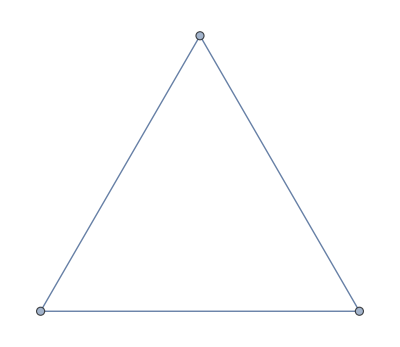
```mathematica
lamanListDB[3]=<|2->{-Graphics-}|>;
```

3 - Laman graph are

```mathematica
(*{Graph[{1<->2}],lamanListDB[4][[2]],lamanListDB[6][[2]],lamanListDB[8][[2]]}//Flatten*)
```

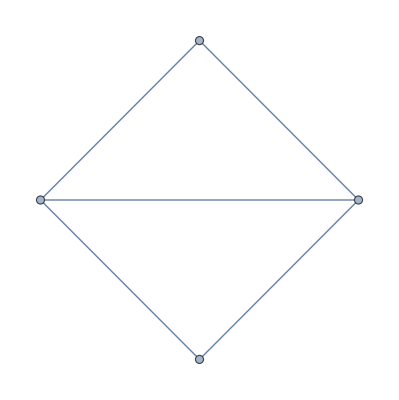
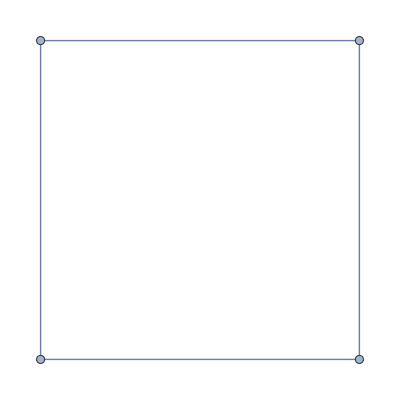
```mathematica
lamanListDB[4]=<|2->{-Graphics-},3->{-Graphics-}|>;
```

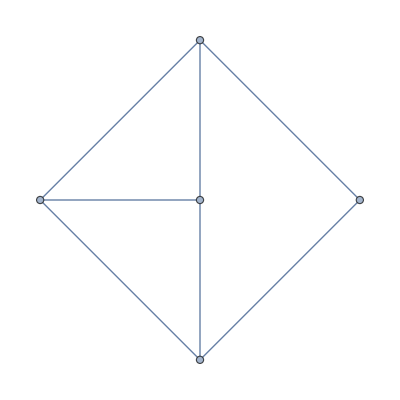
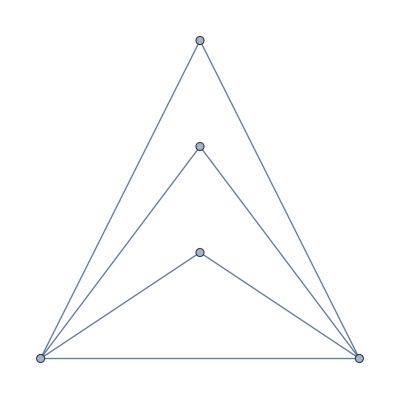
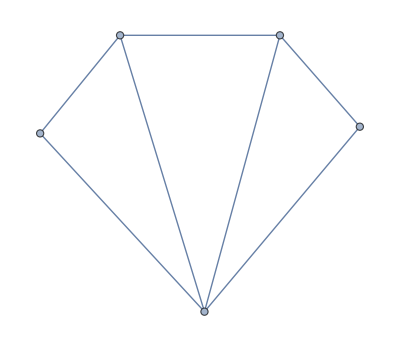
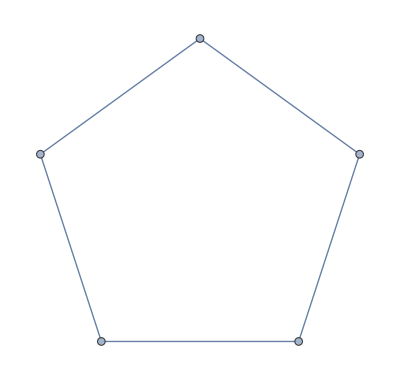
```mathematica
lamanListDB[5]=<|2->{-Graphics-,-Graphics-,-Graphics-},4->{-Graphics-}|>;
```

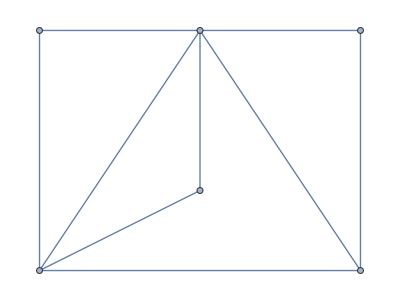
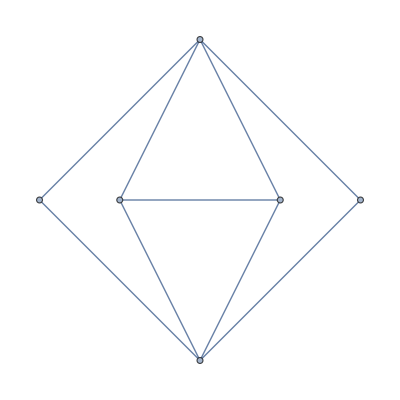
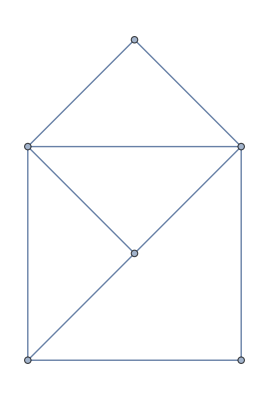
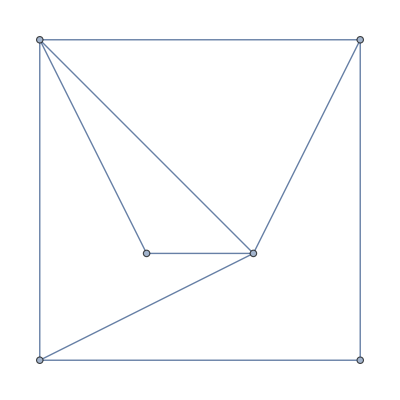
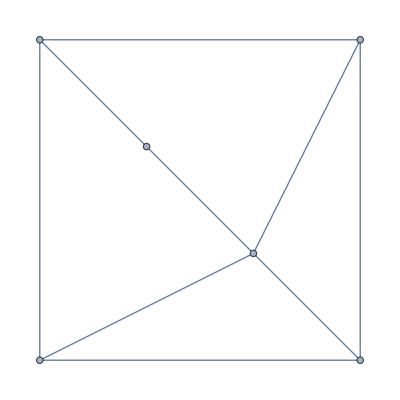
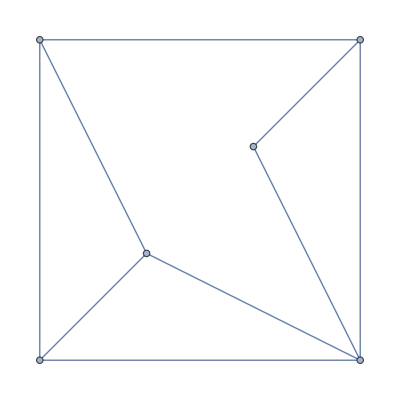
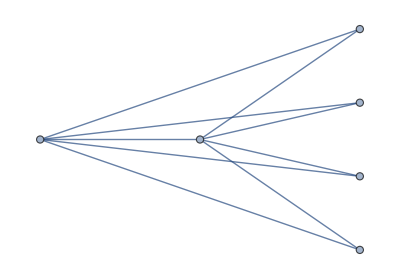
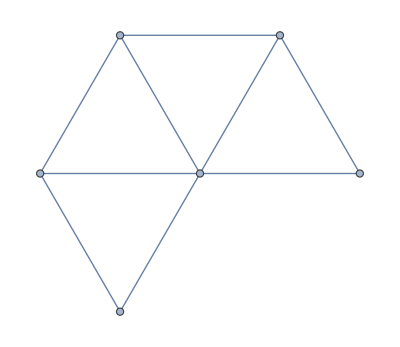
```mathematica
lamanListDB[6]=<|2->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},3->{-Graphics-,-Graphics-},5->{-Graphics-}|>;
```

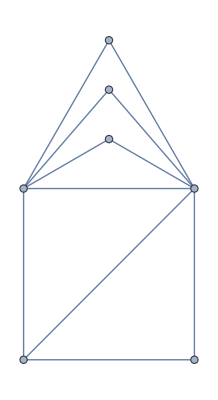
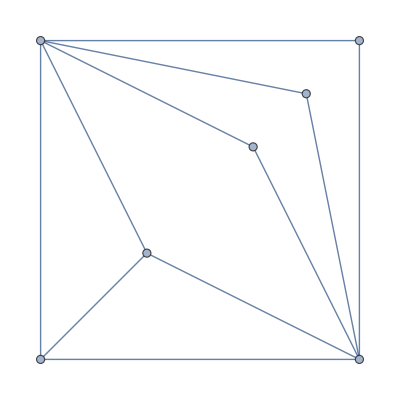
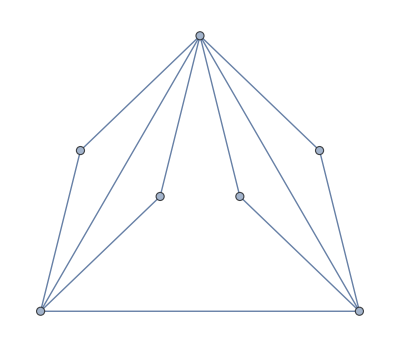
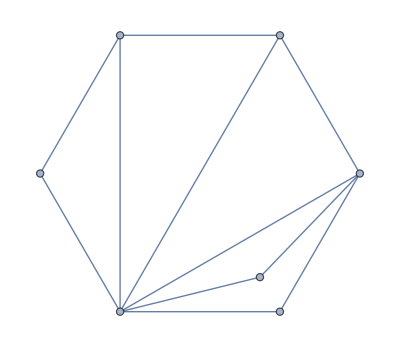
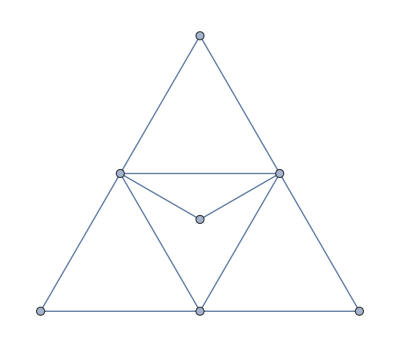
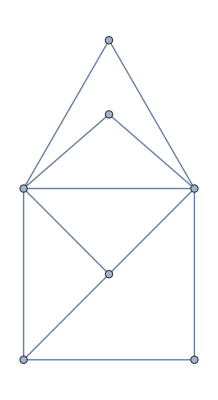
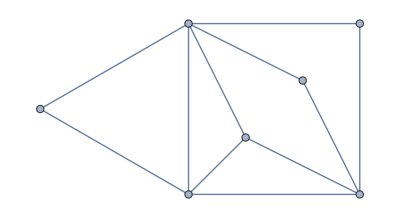
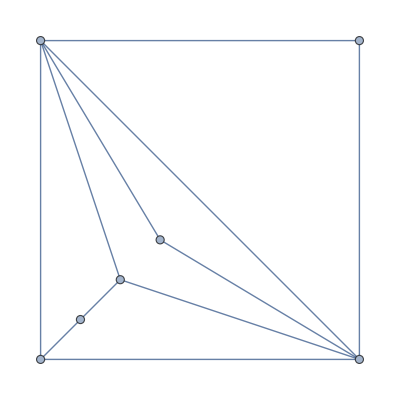
```mathematica
lamanListDB[7]=<|2->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},6->{-Graphics-}|>;
```

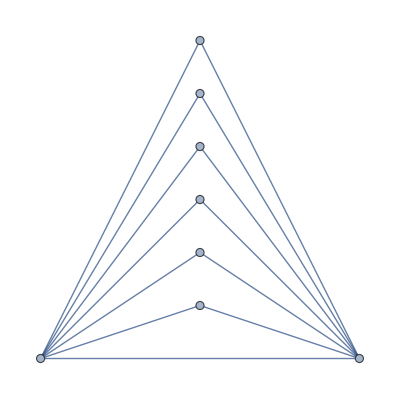
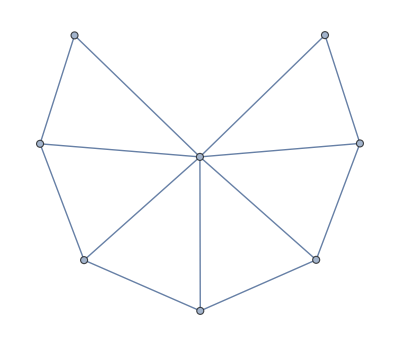
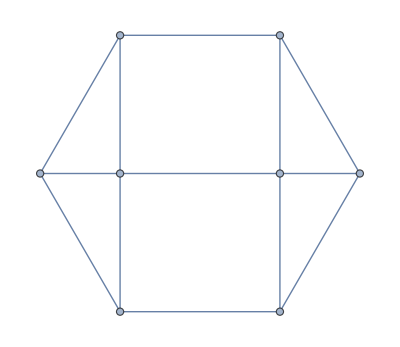
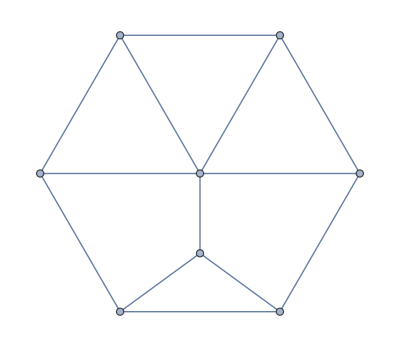
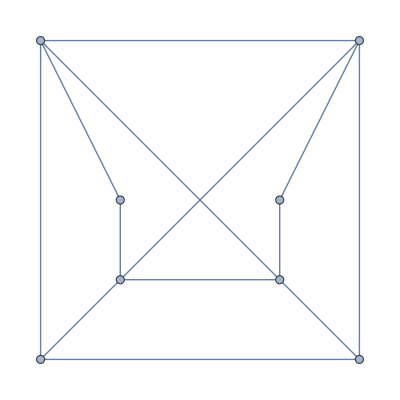
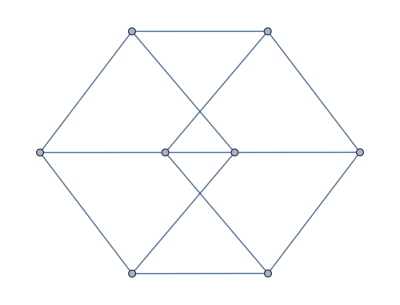
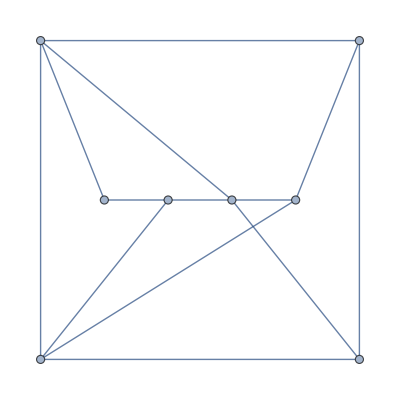
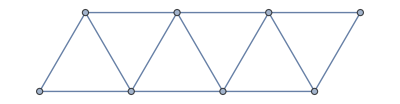
```mathematica
lamanListDB[8]=<|2->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},3->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},4->{-Graphics-,-Graphics-}|>;
```

```mathematica
lamanListDB[9]=<|2->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>;
```

```mathematica
lamanListDB[10]=<|2->{-Graphics-,-Graphics-,-Graphics-,-Graphics-},3->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},5->{-Graphics-}|>;
```

```mathematica
lamanListDB[11]=<|2->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>;
```

```mathematica
lamanListDB[12]=<|2->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},3->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>;
```

```mathematica
lamanListDB[13]=<||>;
```

```mathematica
lamanListDB[14]=<|2->{-Graphics-,-Graphics-},3->{-Graphics-,-Graphics-},5->{-Graphics-,-Graphics-}|>;
```

```mathematica
lamanListDB[15]=<|2->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>;
```